# The highway to hell

## Menschen machen seltsame Sachen

Staus entwickeln sich aus dem Nichts.

Die Hälfte der Deutschen verbringen jedes Jahr im Durchschnitt 40 Stunden im Stau. 

Oft bilden sich diese Staus aus dem Nichts. Das Nagel-Schreckenberg-Modell simuliert und analysiert den Verkehr unfallfrei und liefert u.A. eine Erklärung für dieses Phänomen. 

Das NaSch-Modell teilt die Straße in einzelne Abschnitte, die entweder von einem Auto besetzt oder leer sind. Diese Zellen haben eine Länge von 7,5 m. Auch die Zeitschritte in Sekunden, oft "Runden" genannt, und Geschwindigkeiten sind diskret, mit Geschwindigkeiten von üblicherweise 0 bis 5. Hierbei ist v=0 ein stehendes Auto, v=1 bedeutet eine Zelle pro Zeitschritt, also 7,5m/s bzw. 27km/h. Somit ist die Maximalgeschwindigkeit v=5 umgerechnet 135km/h. 

Für eine bessere Lesbarkeit unseres Projekts wird ein Download des benötigten Fonts über den Link https://www.dafontfree.co/downloads/ac-dc/ empfohlen.

## Nasch-Modell

Es wird das Haupt Modell geschrieben und Geplottet.
Es besteht aus einer For-Schleife, indem die Schritte für jede runde von i=0 bis zum i=tMax entfaltet werden.
Diese sind die Beschleunigung von jedem Auto um 1. Falls der Abstand von dem nächsten Auto kleiner als die neue Geschwindigkeit ist, wird abgebremst. Außerdem kann ein Auto mit einer Trödelwahrscheinlichkeit p noch zusätzlich abbremsen. Die Autos Fahren in einem ring.
Diese Model wird wieder in jede Modul geschrieben um den unterschiedlichen Übungen schreiben und plotten zu können

```mathematica
(*Modul Nagel-Schreckenberg Modell*)
NaSch[nCar_,nCells_,tMax_,vMax_,p_]:=Module[
(*Eingabe Anzahl der Autos nCar, Anzahl der Zellen nCells, Simulationsdauer tMax, 
Maximalgeschwindigkeit vMax und Trödelwahrscheinlichkeit p mit Funktionsaufruf*)

(*lokale Variablen*)
{xAutos,vAutos,dAutos,minAuto,maxAuto},

(*Listen für x, v und d für Berechnungen außerhalb des Moduls*)
xnasch={};
vnasch={};
dnasch={};

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
xAutos=Sort[RandomSample[Range[nCells],nCar]];
(*erzeugt zufällige (Random) Liste xAutos ohne Wiederholungen (Sample) in aufsteigender Reihenfolge (Sort)*)
vAutos=RandomInteger[{1,vMax},nCar];
(*ordnet jedem Auto eine zufällige Geschwindigkeit von 0 bis vMax zu*)
(*Einzelne Autos sind gekennzeichnet durch Element-Position in der Liste mit Position xAutos[[n]] und Geschwindigkeit vAutos[[n]]*)

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=1,i<=tMax,i++, (*Schleife der Runden bis tMax*)

(*Oft verwendete Variablen*)
minAuto=Min[xAutos];
maxAuto=Max[xAutos];

(*Freie Zellen d vor dem Auto bis zum vorderen*)
dAutos=Table[If[xAutos[[n]]<maxAuto,xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+minAuto-1],{n,nCar-1}]; (*In Schleife, damit es geupdatet wird*)
(*berechnet freie Zellen zum vorderen Auto normal außer für Autos außer dem mit höchster Positition - da Ringstraße sind die freien Zellen geringer als xAutos[[n+1]]-xAutos[[n]]-1*)
(*Arrays starten mit Element 1; n+1 muss für das letzte gleich nCar sein*)
AppendTo[dAutos,If[xAutos[[nCar]]<maxAuto,xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+minAuto-1]];
(*Abstand des Autos an letzter Stelle in Liste zum ersten wird angehängt*)

(*R1: Beschleunigen, falls vMax noch nicht erreicht*)
vAutos=Table[Min[vAutos[[n]]+1,vMax],{n,nCar}];

(*R2: Abbremsen, falls v größer als Abstand d*)
vAutos=Table[Min[dAutos[[n]],vAutos[[n]]],{n,nCar}]; 

(*R3: Trödeln mit Wahrscheinlichkeit p*)
vAutos=Table[If[RandomReal[{0,1}]<=p,vAutos[[n]]=Max[vAutos[[n]]-1,0],vAutos[[n]]],{n,nCar}]; (*Trödeln solange noch nicht v=0*)
(*Falls zufällige Zahl nicht im gegebenen Intervall, bleibt v gleich*)

(*R4: Fahren um vAutos Zellen*)
xAutos=Table[If[xAutos[[n]]+vAutos[[n]]<=nCells,xAutos[[n]]=xAutos[[n]]+vAutos[[n]],xAutos[[n]]=xAutos[[n]]+vAutos[[n]]-nCells],{n,nCar}];
(*Falls Autos außerhalb Zellen bewegt, wird Bewegung in erster Zelle fortgesetzt, da Ringstraße*)
(*Aktualisieren der Positionen nicht anhand Verschieben der Autos innerhalb der Liste, sondern durch Verändern der Einträge in xAutos*)

(*Abspeichern in globale Variablen*)
AppendTo[xnasch,xAutos];
AppendTo[vnasch,vAutos];
AppendTo[dnasch,dAutos];
];
Return[{xnasch,vnasch}]
]
```

```mathematica
NaSch[100,300,100,5,0.15];
```

```mathematica
(*Grafische Darstellung Straße*)
densityplot:=Module[
{nCar,nCells,tMax,p,strasse,newstrasse},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCar=100;
nCells=300;
tMax=100;
p=0.15;

(*Sortierte Liste der Straße mit leeren Zellen als 0 und besetzt als 1*)
strasse=Table[Table[If[Select[xnasch[[m]],#==n &]=={},0,1],{n,1,nCells}],{m,tMax}];

(*Anpassen strasse sodass t in positive x-Richtung läuft statt in positiver y-Richtung*)
newstrasse=Table[Table[strasse[[n,m]],{n,tMax}],{m,nCells}];

(*ListDensityPlot*)
listdensityplot=ListDensityPlot[newstrasse,FrameLabel->{"Zeit t","Zellen der Straße"},ImageSize->Medium,
PlotLabel->"Grafische Darstellung der Straße mit "<>ToString[nCar]<>" Autos und p="<>ToString[p]];
Return[listdensityplot]
]
```

```mathematica
densityplot;
Show[listdensityplot]
```

-Graphics-

## Dichteplot

Der Nächste Modul entspricht den dichteplot. es werden eine bestimmte Anzahl an Zelle beobachtet, sonst würde die dichte immer gleich. Die dichte entspricht der Anzahl an Autos die an dem entsprechenden Runde in diesen Intervall Zellen gefahren sind.

Im Dichteplot wird die Anzahl der Autos N über einer Anzahl avCells Zellen berechnet und über der Zeit t dargestellt.

```mathematica
(*Dichteplot über Zeit*)
dichteplot[avCells_]:=Module[
(*lokale Variablen*)
{nCar,nCells,tMax,avstrasse,newavstrasse,tavstrasse,anzahl,laengen,iter,t,cell},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCar=100;
nCells=300;
tMax=100;

(*Liste Anzahl Autos innerhalb Intervall avCells und das pro Zeitschritt*)
laengen={};

(*Anzahl der Intervalle avCells in nCells=iter, Anzahl Autos innerhalb Intervall=anzahl*)
iter=0;t=1;anzahl=0;
(*For-Schleife für einzelne Intervalle mit Länge avCells*)
For[cell=1+iter,cell<=avCells+iter,cell++,
(*Falls Auto auf Zelle, Anzahl erhöhen*)
If[Select[xnasch[[t]],#==cell &]!={},anzahl=anzahl+1,anzahl=anzahl];
(*Falls letzte Zelle des Intervalls betrachtet, Anzahl abgespeichert, wieder auf 0*)
If[Divisible[cell,avCells],
AppendTo[laengen,anzahl];
anzahl=0;
(*Falls letzte Subliste in xnasch betrachtet, nächsten Intervall betrachten ab erster Subliste mit t=0*)
If[t==tMax,
(iter=iter+avCells;
If[iter>nCells-avCells,Break[]];
t=1;),
(*Sonst: nächste Subliste betrachten mit gleichem Intervall*)
t=t+1;];
(*Betrachten erste Zelle im Intervall für nächsten Durchgang*)
cell=1+iter;
];
];
(*Ergebnis ist Liste mit Anzahlen der Autos von Zelle 0 bis avCells für t=1,2,3,..., dann von Zelle avCells+1 bis 2 avCells usw.*)
(*Aufteilen laengen in Sublisten für die Intervalle*)
laengen=Partition[laengen,tMax];

listdichteplot=ListDensityPlot[laengen,FrameLabel->{"Zeit t","Intervalle"},ImageSize->Medium,
PlotLabel->"Dichteplot über Zeit t mit Intervalllänge "<>ToString[avCells],PlotLegends->Automatic];
Return[listdichteplot]
]
```

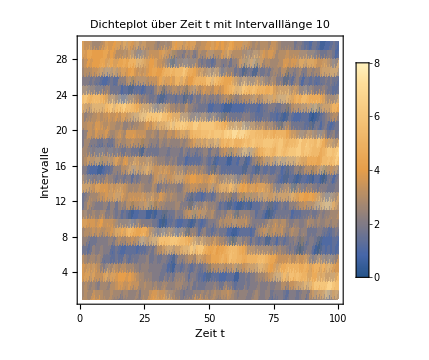

```mathematica
dichteplot[10];
Show[listdichteplot]
```

Das Dichteplot stellt die Straße über die Zeit dar. Auf der y-Achse sind die Zellen der Straße mit besetzten Zellen als helle Punkte und leere als dunkelblaue Punkte. Die Entwicklung über die Zeit ist in positiver x-Richtung aufgetragen. Es lässt sich beobachten, dass eine Ansammlung von Autos bei t=0 in der Grafik in positiver x-Richtung nach unten wandert, indem Autos aus den vorderen Zellen der Ansammlung losfahren und die hinteren sich stauen bzw neue Autos auf den Stau auffahren.

## Histogramme

In diesem Modul werden erzeugt die Histogramme der Geschwindigkeit und den Abstand für einen Zeitpunkt tMax.

```mathematica
(*Histogramme Geschwindigkeiten und Abstand für einen Zeitpunkt*)
vdhisto[carlist_,tlist_]:=Module[
(*tlist sind Zeitpunkte, für die Histogramme zu bestimmen sind; auch einzelnen Zeitpunkt als Liste eingeben*)

(*lokale Variablen*)
{nCells,nCar,tMax,vMax,p,anzahlt,anzahlcars,zeit,viAutos,diAutos,i,vhisto,dhisto},

(*Variablen aus vorherigem NaSch-Aufruf*)
nCells=300;
tMax=100;
vMax=5;
p=0.15;

(*Listen der Plots*)
histoplot={};
anzahlt=Length[tlist];
anzahlcars=Length[carlist];

(*Für betrachtete Anzahlen Autos*)
For[k=1,k<=anzahlcars,k++,
(*Anzahl Autos*)
nCar=carlist[[k]];
(*Berechnen xnasch, vnasch und dnasch*)
NaSch[nCar,nCells,tMax,vMax,p];

For[j=1,j<=anzahlt,j++,
(*Betrachtete Zeit*)
zeit=tlist[[j]];
(*Listen Autos mit Geschwindigkeiten v=0,1,2,3,4,5*)
Clear[viAutos];
viAutos=Table[Select[Table[vnasch[[zeit,n]],{n,1,nCar}],#==i &],{i,0,5}];

(*Listen Abstände d=0,1,...,nCar*)
Clear[diAutos];
diAutos=Select[Table[Select[Table[dnasch[[zeit,n]],{n,1,nCar}],#==i &],{i,0,Max[dnasch[[zeit]]]}],UnsameQ[#, {}] &]; 
(*Löschen der Abstände, die nicht vorkommen*)

AppendTo[histoplot,Histogram[viAutos,{1},AxesLabel->{v,Anzahl Autos mit Indexed[v,"i"]},ColorFunction->"Pastel",PlotRange->{{Automatic,5.5},Automatic},ImageSize->Medium,
PlotLabel->"Histogramm von v mit "<>ToString[nCar]<>" Autos, t="<>ToString[zeit]<>" und p="<>ToString[p]]];
AppendTo[histoplot,Histogram[diAutos,{1},AxesLabel->{d,Anzahl Autos mit Indexed[d,"i"]},ColorFunction->"Pastel",PlotRange->{0,All},ImageSize->Medium,
PlotLabel->"Histogramm von d mit "<>ToString[nCar]<>" Autos, t="<>ToString[zeit]<>" und p="<>ToString[p]]];
(*Histogramm zählt, wie oft eine Zahl in einer Liste und den Sublisten darin vorkommt*)
];];
Return[{histoplot}]
]
```

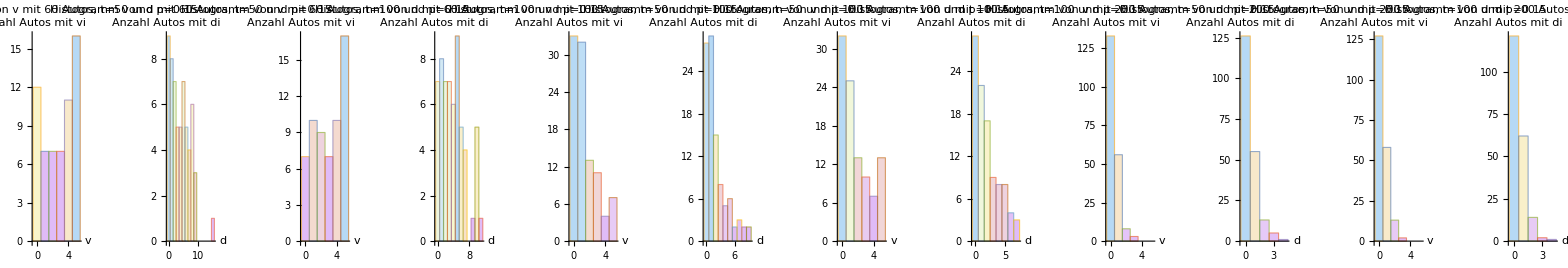

```mathematica
vdhisto[{60,100,200},{50,100}];
GraphicsGrid[{histoplot},Spacings->Scaled[.5]]
```

Aus dem erster Histogramm kann beobachtet werden, dass je größer der Abstand zwischen den Autos ist, desto weniger Autos mit diesem Abstand vorhanden sind wegen den Anzahl an Zellen und die Verteilung des Autos.
Der zweiter Histogramm zeigt dass mehrere Autos die Geschwindigkeit 1 oder 0 besitzen und  weniger sind die Autos mit höhere Geschwindigkeit, weil weniger Autos höhere Abstände als 1 oder 0 besitzen.

## Meanvarfluss

Hier werden: die mittlere Geschwindigkeit der Autos, 
die Varianz des Abstands zwischen jedes Auto, und den Verkehrsfluss, für jede runde berechnet.
Die Verkehrsflüsse ist die Anzahl an Auto die durch die letzte Zelle fahren, pro Zeitschritt kann es mit einer Spur also entweder 0 oder 1 sein.
Anschließend werden die Grafiken von Geschwindigkeit und die Varianz geplottet und dann die korreliert. Der Fluss wird auch dargestellt.

```mathematica
(*Berechnung mittlere v über t, Varianz des mittleren Abstands und des Verkehrsflusses über t*)
Meanvarfluss[nCar_,nCells_,tMax_,vMax_,p_]:=Module[
(*betrachtete Zelle ist letzte Zelle der Straße*)

(*lokale Variablen*)
{xAutos,vAutos,dAutos,vMittel,dVar,savefluss,savexAutos,m},

(*NaSch-Modell*)

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
xAutos=Sort[RandomSample[Range[nCells],nCar]];
vAutos=RandomInteger[{1,vMax},nCar]; 

(*Erzeugen einelementige Liste mit vMittel, dVar und fluss*) 
Clear[vMittel];
vMittel=Table[Nothing,{n,1}];
dVar=Table[Nothing,{n,1}];
savefluss=Table[Nothing,{n,1}];

(*Liste zum Speichern von xAutos aus dem vorherigen Zeitschritt*)
savexAutos=xAutos;
(*Index zum Überprüfen der Positionen, startet von der überprüften Zelle nCells*)(*Fluss als Durchfluss von Position nCells zu 1*)
m=nCar;

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=0,i<=tMax,i++, 

(*Freie Zellen d vor dem Auto bis zum vorderen*)
dAutos=Table[If[xAutos[[n]]<Max[xAutos],xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+Min[xAutos]-1],{n,nCar-1}]; 
AppendTo[dAutos,If[xAutos[[nCar]]<Max[xAutos],xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+Min[xAutos]-1]];

(*R1: Beschleunigen, falls vMax noch nicht erreicht*)
vAutos=Table[Min[vAutos[[n]]+1,vMax],{n,nCar}];

(*R2: Abbremsen, falls v größer als Abstand d*)
vAutos=Table[Min[dAutos[[n]],vAutos[[n]]],{n,nCar}]; 

(*R3: Trödeln mit Wahrscheinlichkeit p*)
vAutos=Table[If[RandomReal[{0,1}]<=p,vAutos[[n]]=Max[vAutos[[n]]-1,0],vAutos[[n]]],{n,nCar}]; 

(*R4: Fahren um vAutos Zellen*)
xAutos=Table[If[xAutos[[n]]+vAutos[[n]]<=nCells,xAutos[[n]]=xAutos[[n]]+vAutos[[n]],xAutos[[n]]=xAutos[[n]]+vAutos[[n]]-nCells],{n,nCar}];

(*Verkehrsfluss durch letzte Zelle*)
(*Überprüft, ob Auto mit höchster Position über Straßenende hinaus auf den Anfang zurück gefahren ist 
ja: nächst niedrigeres Auto wird betrachtet + fluss 1 hinzufügen, 
nein: Auto wird weiter betrachtet + fluss 0 hinzufügen
Index m geht Autos vom letzten Element bis zum ersten durch, danach wieder Start bei letztem*)
If[m==0,m=nCar,m=m];
If[xAutos[[m]]<savexAutos[[m]],
AppendTo[savefluss,1];
m=m-1;,
AppendTo[savefluss,0];
];
Clear[savexAutos];
savexAutos=xAutos;

(*mittlere Geschwindigkeit*)
AppendTo[vMittel, N[Mean[vAutos],6]];
(*Varianz dAutos*)
AppendTo[dVar, N[Variance[dAutos],6]];

];
ResourceFunction["PlotGrid"][{
{ListPlot[vMittel,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"mittlere Geschwindigkeit "OverBar[v]}]},
{ListPlot[dVar,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"Varianz des Abstands d"}]},
{ListPlot[savefluss,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"Fluss pro Zeitschritt"}]}
},
ImageSize->Large,FrameLabel->{"Zeit t",None}
]

(*Korrelation mittlere Geschwindigkeit und Varianz des Abstands*)
ListPlot[Thread[{dVar,vMittel}],ImageSize->Medium,ColorFunction->"Rainbow",Frame->True,FrameLabel->{"Varianz des Abstands d","mittlere Geschwindigkeit " OverBar[v]},
PlotLabel->"Korrelation Varianz des Abstands und mittlere Gewschindigkeit"]
]
```

```mathematica
Meanvarfluss[100,300,100,5,0.15]
```

Die Grafiken von Mittlere Geschwindigkeit, Varianz des Abstands und Der Fluss pro Zeitschritt sind über die Zeit dargestellt. Die Zeigen dass die mittlere Geschwindigkeit und die Varianz des abstand haben größere Sprunge. Die Geschwindigkeit variiert zwischen 1 und 2 das bedeutet, dass wann die niedriger werden sich Staus bilden.
Die Sprünge von Varianz sind schon höher als die von der Geschwindigkeit, von 2 bis ungefähr 10. Die meisten punkte befinden sich um die Varianz herum die in der Mitte zwischen der niedrigste und die höchste Varianz liegt.
Die Grafik der Fluss zeigt, wie das nur 1 oder 0 sein kann weil nur eine spur simuliert wird. Da ein Auto nur bis zu einer Zelle vor dem nächsten fahren kann (R2: Abbremsen, falls v größer als d), kann eine Zelle in einer Runde nur von einem Auto durchquert werden.
Aus der Korrelation der Geschwindigkeit und der Varianz des Abstands ist zu sehen, wie die mittlere Geschwindigkeit linear abnimmt mit der Zunahme von der Varianz des Abstands.

## Fundamentalplot

Unter fundamental Plot versteht man die Korrelation zwischen Verkehrsfluss über die dichte.
In diesem Teil wird ein Modul dafür hergestellt und anschließend das dargestellt.
Nachdem wird es für unterschiedliche Trödelwahrscheinlichkeiten p geschrieben und geplottet.

```mathematica
(*Fundamentalplot*)
FundamentalD[nCells_,tMax_,vMax_,p_]:=Module[
(*Fluss wird für Dichten 0 bis 1 berechnet*)

(*lokale Variablen*)
{xAutos,vAutos,dAutos,nCar,density,addfluss,savexAutos,m,fluss},

(*Erzeugen einelementige Liste mit Dichte, Fluss, und Fluss für jede Anzahl an Autos*) 
density=Table[Nothing,{n,1}];
fluss=Table[Nothing,{n,1}];

(*NaSch-Modell*)

(*Schleife für ansteigende Dichte/Anzahlen an Autos*)
For[nCar=0,nCar<=nCells,nCar++,

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
xAutos=Sort[RandomSample[Range[nCells],nCar]];
vAutos=RandomInteger[{1,vMax},nCar]; 

(*Liste zum Speichern von xAutos aus dem vorherigen Zeitschritt*)
savexAutos=xAutos;
(*Index zum Überprüfen der Positionen, startet von der überprüften Zelle nCells*)(*Fluss als Durchfluss von Position nCells zu 1*)
m=nCar;
addfluss=0;

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=0,i<=tMax,i++, 

(*Freie Zellen d vor dem Auto bis zum vorderen*)
dAutos=Table[If[xAutos[[n]]<Max[xAutos],xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+Min[xAutos]-1],{n,nCar-1}]; 
AppendTo[dAutos,If[xAutos[[nCar]]<Max[xAutos],xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+Min[xAutos]-1]];

(*R1: Beschleunigen, falls vMax noch nicht erreicht*)
vAutos=Table[Min[vAutos[[n]]+1,vMax],{n,nCar}];

(*R2: Abbremsen, falls v größer als Abstand d*)
vAutos=Table[Min[dAutos[[n]],vAutos[[n]]],{n,nCar}]; 

(*R3: Trödeln mit Wahrscheinlichkeit p*)
vAutos=Table[If[RandomReal[{0,1}]<=p,vAutos[[n]]=Max[vAutos[[n]]-1,0],vAutos[[n]]],{n,nCar}]; 

(*R4: Fahren um vAutos Zellen*)
xAutos=Table[If[xAutos[[n]]+vAutos[[n]]<=nCells,xAutos[[n]]=xAutos[[n]]+vAutos[[n]],xAutos[[n]]=xAutos[[n]]+vAutos[[n]]-nCells],{n,nCar}];

(*Verkehrsfluss durch letzte Zelle -> Anzahl Autos durch Zelle pro Zeitschritt*)
If[m==0,m=nCar,m=m];
If[xAutos[[m]]<savexAutos[[m]],
addfluss=addfluss+1;
m=m-1;,
addfluss=addfluss;
];
Clear[savexAutos];
savexAutos=xAutos;
];

(*Dichte über die gesamte Straße*)
AppendTo[density,nCar/nCells];

(*Verkehrsfluss für Dichte nCar/nCells*);
AppendTo[fluss,addfluss];
];
(*Fundamentalplot mit addfluss*);
ListPlot[Thread[{density,fluss/tMax}],ImageSize->Medium,PlotRange->{0,0.9},Frame->True,FrameLabel->{"Dichte ρ","Zeitliches Mittel des Flusses mit p = " <> ToString[p]},
PlotStyle->RandomChoice[{Red,Orange,Yellow,LightGreen,LightBlue,Blue,Purple,Pink}]] (*Punkte hell für dunklen Hintergrund in späterem Notebook*)
]
```

```mathematica
FundamentalD[300,100,5,0]
FundamentalD[300,100,5,0.1]
FundamentalD[300,100,5,0.15]
FundamentalD[300,100,5,0.2]
FundamentalD[300,100,5,0.25]
FundamentalD[300,100,5,0.3]
FundamentalD[300,100,5,0.5]
FundamentalD[300,100,5,0.75]
FundamentalD[300,100,5,1]
```

Man sieht aus die Fundamentalplots, dass je höher die Trödelwarscheinligkeit ist desto höher ist die Streuung des Flusses und desto geringere ist der Fluss.
Die Diagramme zeigen wie die Höhe der Peaks beim p=0.1 am höchsten ist, und zwar fast bis 0.7 und dass beim p= 1 viel geringer wird, also bis ungefähr 0,012 hoch werden. 
Mit eine unterschied von Δp=0.05 unterscheid sich den peak von 0.5 und mit Δp=0.1 wird das unterschied auch beim ungefähr 0.1
Man kann beobachten, dass bis dichte, ungefähr, 0.125 wird der Fluss linear erhöhen, weil keine Staus noch gibt's und nach diese dichte werden mehrere Staus sich entwickeln und wird damit der Fluss linear abfallen. Der Fluss wird 0 ungefähr bei dichte=1.
Eine Ausnahme bildet sich für p=1 wo der Fluss fast sofort abfällt, also ab eine dichte nah an 0.

## VDR

In dieses Modul wird der Nasch- Modell in VDR geschrieben, und zwar mit einer Geschwindigkeit das abhängig von der Trödelwahrscheinlichkeit variiert, also wenn die Geschwindigkeit null ist wird die Trödelwahrscheinligkeit um q höher als sonst.

```mathematica
(*Fundamentalplots des Velocity-Dependent-Randomization Modells*)
vdrNaSch[nCells_,tMax_,vMax_,q_]:=Module[
(*q ist zusätzliche Wahrscheinlichkeit zum Trödeln beim Anfahren*)

(*lokale Variablen*)
{xAutos,vAutos,dAutos,nCar,p,a,density,addfluss,savexAutos,m,fluss,posxAutos,newposübert,posübert,rhoplot,dichte,viAutos,diAutos,vhisto,dhisto},

(*Leere Liste für Plots*)
densplot=Table[Nothing,{n,1}];
histoplot=Table[Nothing,{n,1}];
fundplot=Table[Nothing,{n,1}];

(*Histogramme für 3 Dichten*)
rhoplot={60,100,200};

(*Trödelwahrscheinlichkeiten pi*)
p={0.15,0.3};
a=1;
(*Ausführen für Trödelwahrscheinlichkeiten p*)
Do[
((*Erzeugen einelementige Liste mit Dichte, Fluss, und Fluss für jede Anzahl an Autos*) 
Clear[density];
density=Table[Nothing,{n,1}];
Clear[fluss];
fluss=Table[Nothing,{n,1}];

(*Schleife für ansteigende Dichte/Anzahlen an Autos*)
For[nCar=0,nCar<=nCells,nCar++,

(*Leere Listen für ListDensityPlot*)
posxAutos=Table[Nothing,{n,1}];
newposübert=Table[Nothing,{n,1}];
posübert=Table[Nothing,{n,1}];

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
xAutos=Sort[RandomSample[Range[nCells],nCar]];
vAutos=RandomInteger[{1,vMax},nCar];

(*Liste zum Speichern von xAutos aus dem vorherigen Zeitschritt*)
savexAutos=xAutos;
(*Index zum Überprüfen der Positionen, startet von der überprüften Zelle nCells*)(*Fluss als Durchfluss von Position nCells zu 1*)
m=nCar;
addfluss=0;

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=0,i<=tMax,i++, 

(*Freie Zellen d vor dem Auto bis zum vorderen*)
dAutos=Table[If[xAutos[[n]]<Max[xAutos],xAutos[[n+1]]-xAutos[[n]]-1,nCells-xAutos[[n]]+Min[xAutos]-1],{n,nCar-1}];
AppendTo[dAutos,If[xAutos[[nCar]]<Max[xAutos],xAutos[[1]]-xAutos[[nCar]]-1,nCells-xAutos[[nCar]]+Min[xAutos]-1]];

(*R1: Beschleunigen, falls vMax noch nicht erreicht*)
vAutos=Table[Min[vAutos[[n]]+1,vMax],{n,nCar}];

(*R2: Abbremsen, falls v größer als Abstand d*)
vAutos=Table[Min[dAutos[[n]],vAutos[[n]]],{n,nCar}]; 

(*R3: Trödeln mit Wahrscheinlichkeit p*)(*Randomization, q=p0-p, p+q wahrscheinlichkeit dass sie trödeln falls die vorher v=0 hatten, p=wahrsch. v>0*)
vAutos=Table[If[vAutos[[n]]==0,If[RandomReal[{0,1}]<=p[[a]]+q,vAutos[[n]],vAutos[[n]]],If[RandomReal[{0,1}]<=p[[a]],vAutos[[n]]=vAutos[[n]]-1,vAutos[[n]]]],{n,nCar}];
(*Wenn Auto steht ist p um q erhöht*)

(*R4: Fahren um vAutos Zellen*)
xAutos=Table[If[xAutos[[n]]+vAutos[[n]]<=nCells,xAutos[[n]]=xAutos[[n]]+vAutos[[n]],xAutos[[n]]=xAutos[[n]]+vAutos[[n]]-nCells],{n,nCar}];

(*VDR: beim Anfahren nur mit einer Wahrscheinlichkeit p+q anfahren -> lieber im Modul festlegen?*)

(*Verkehrsfluss durch letzte Zelle -> Anzahl Autos durch Zelle pro Zeitschritt*)
If[m==0,m=nCar,m=m];
If[xAutos[[m]]<savexAutos[[m]],
addfluss=addfluss+1;
m=m-1;,
addfluss=addfluss;
];
Clear[savexAutos];
savexAutos=xAutos;

(*ListDensityPlot*)
If[MemberQ[rhoplot,nCar],
posxAutos=Flatten[Table[If[Select[xAutos,#==n &]=={},0,1],{n,1,nCells}]];
(*Positionen der Autos für den DensityPlot abspeichern*)
AppendTo[posübert,posxAutos]
];
];
(*Dichte über die gesamte Straße*)
AppendTo[density,nCar/nCells];

(*ListDensityPlot für 100 Autos*)
If[nCar==100,
(*Anpassen posübert sodass t in positive x-Richtung läuft statt in positiver y-Richtung*)
newposübert=Table[Table[posübert[[n,l]],{n,tMax}],{l,nCells}];
Clear[dichte];
dichte=DecimalForm[nCar/nCells,2];
AppendTo[densplot,ListDensityPlot[newposübert,FrameLabel->{"Zeit t","Zellen der Straße"},ImageSize->Medium,PlotLabel->"Dichteplot für "<>ToString[nCar]<>" Autos, p = "<>ToString[p[[a]]]<>" und q = "<>ToString[q]]];
];

(*Histogramme für 60, 100 und 200 Autos*)
If[MemberQ[rhoplot,nCar],
(*Listen Autos mit Geschwindigkeiten v=0,1,2,3,4,5*)
viAutos=Table[Select[Table[vAutos[[n]],{n,1,nCar}],#==i &],{i,0,5}];

(*Listen Abstände d=0,1,...,nCar*)
diAutos=Select[Table[Select[Table[dAutos[[n]],{n,1,nCar}],#==i &],{i,0,Max[dAutos]}],UnsameQ[#, {}] &]; 
(*Löschen der Abstände, die nicht vorkommen*)

AppendTo[histoplot,Histogram[viAutos,{1},AxesLabel->{v,Anzahl Autos mit Indexed[v,"i"]},ColorFunction->"Pastel",PlotRange->{{Automatic,5.5},Automatic},ImageSize->Medium,
PlotLabel->"Histogramm von v für "<>ToString[nCar]<>" Autos, p = "<>ToString[p[[a]]]<>" und q = "<>ToString[q]]];
AppendTo[histoplot,Histogram[diAutos,{1},AxesLabel->{d,Anzahl Autos mit Indexed[d,"i"]},ColorFunction->"Pastel",PlotRange->{0,All},ImageSize->Medium,
PlotLabel->"Histogramm von d für "<>ToString[nCar]<>" Autos, p = "<>ToString[p[[a]]]<>" und q = "<>ToString[q]]];
(*Histogramm zählt, wie oft eine Zahl in einer Liste und den Sublisten darin vorkommt*)
];

(*Verkehrsfluss für Dichte nCar/nCells*);
AppendTo[fluss,addfluss]; 
];
(*Fundamentalplot mit addfluss*)
AppendTo[fundplot,ListPlot[Thread[{density,fluss/tMax}],ImageSize->Medium,Frame->True,FrameLabel->{"Dichte ρ","Zeitliches Mittel des Flusses"},PlotLabel->"Fundamentalplot mit p= "<>ToString[p[[a]]]<>" und q = "<>ToString[q],
PlotStyle->RandomChoice[{Red,Orange,Yellow,LightGreen,LightBlue,Blue,Purple,Pink}]]]; (*Hell für dunklen Hintergrund in späterem Notebook*)
(*Variable a hochzählen für nächste p*)
a=a+1;
),2];
Return[{histoplot,densplot,fundplot}]
]
```

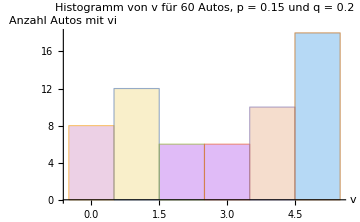
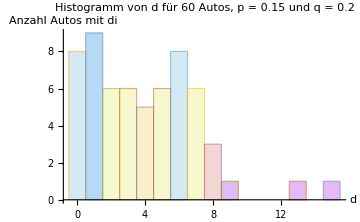
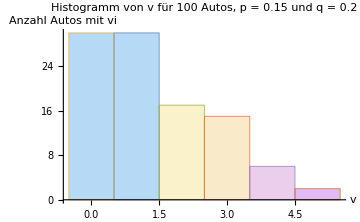
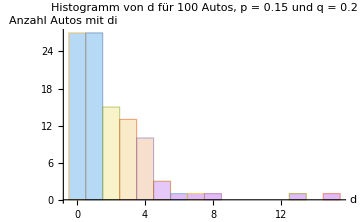
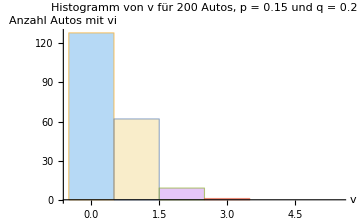
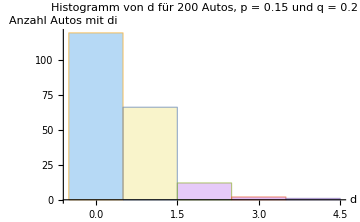
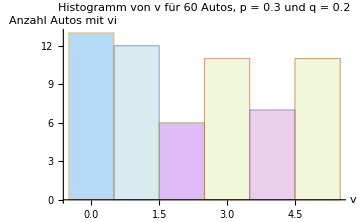
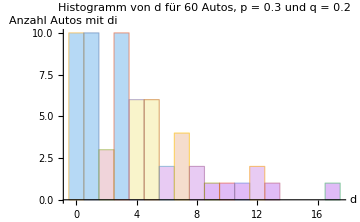
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
vdrNaSch[300,100,5,0.2]
```

Aus den ersten zwei Histogrammen kann gefolgert werden, dass aufgrund von der geringeren Anzahl an Autos (60) über der Anzahl an Zellen (300) die Erhöhung der Trödelwahrscheinlichkeit q nicht häufig vorkommt, weil der Platz zwischen zwei Autos häufig höher ist als dessen Geschwindigkeit. 
Das passiert weniger bei einer höheren Anzahl an Fahrzeugen (z.B. 100 über 300), weil die Abstände geringer sind. Das verursacht eine Erhöhung der Trödelwahrscheinlichkeit um q, weshalb sich bilden Staus bilden. Eine sehr geringere Menge an Autos haben einen größeren Abstand.
Bei 200 Autos ist letzteres nicht mehr erkennbar, die Abstände sind sehr gering.
Aus den nächsten Histogrammen, mit p erhöht zu 0.3, lässt sich beobachten, dass aufgrund der höheren Trödelwahrscheinlichkeit viele Autos eine geringere Geschwindigkeit haben im Vergleich zu p=0.15. 
Aus dem Dichteplot kann beobachtet werden, dass mit einer Wahrscheinlichkeit von p=0.15 die lokale Dichte der Autos mehrmals höher ist, es bilden sich größere Staus. Mit einer Wahrscheinlichkeit p=0.3 ist die lokale Dichte häufig höher auf der ganzen Straße, aber die Staus werden kürzer.
Die Fundamentalplots sehen wie die für 0.15 und 0.3 aus der Fundamentalplots teil (s. oben) aus. Also wird die zusätzliche q nicht in der Grafik viel auswirken.

## Zwei Spuren

Als letzte wird den Model auf zwei Spuren angepasst also wird wieder den nasch Model von Anfang genutzt nicht auf VDR basiert.

```mathematica
(*Modell zwei Fahrspuren*)
twolanesNaSch[nCells_,tMax_,vMax_,p_]:=Module[
(*nCells ist Länge beider Spuren, nCar Anzahl aller Autos für das Histogramm von v *)
(*Für Fundamentalplots eine nCells!=0mod5 eingeben, für Histogramme zusätzlich nCells=0mod5*)

(*lokale Variablen*)
{xAutos,xAutos1,xAutos2,vAutos1,vAutos2,dAutos1,dAutos2,viAutos,viAutos1,viAutos2,diAutos,diAutos1,diAutos2,nCar,density,density1,density2,
fluss,addfluss,savefluss,savefluss1,savefluss2,savexAutos1,savexAutos2,savevAutos1,savevAutos2,m1,m2,l1,l2,savem1,savem2,savel1,savel2,
vMittel,dVar1,dVar2,index1,index2,nachindex1,nachindex2,h,i,j,k,o,r,s,rhoplot,strecke1,strecke2,fahrt1,fahrt2,
vdvardensplot,flussplot,fundplot,histoplot,laengesx1,laengesx2,laengex1,laengex2},

(*Erzeugen einelementige Liste mit Gesamtdichte und Fluss für nCar=0, für jedes nCar werden Werte hinzugefügt*) 
density={0};
fluss={0};

(*Erzeugen Listen für Plots*)
histoplot=Table[Nothing,{n,1}];
vdvardensplot=Table[Nothing,{n,1}];
flussplot=Table[Nothing,{n,1}];

(*Liste Anzahlen Autos, für die Histogramme, dVar, vMittel und der Fluss geplottet werden*)
rhoplot={60,100,200};
Clear[nachindex1];

(*NaSch-Modell*)

(*Schleife für ansteigende Dichte/Anzahlen an Autos*)
For[nCar=1,nCar<=nCells,nCar++, 

(*Autos haben Position x und Geschwindigkeit v zum vorderen Auto*)
(*Erstellen Liste xAutos mit doppelter Länge als Straße*)
xAutos=Sort[RandomSample[Range[2 nCells],nCar]];
(*xAutos1=Sort[RandomSample[Range[nCells],nCar]];
xAutos2=Sort[RandomSample[Range[nCells],nCar]];*)
(*Aufteilen Liste in zwei Spuren, 1 rechts, 2 links*)
xAutos1=Select[xAutos,#<=nCells &];
(*Positionen der linken Spur setzen in Bereich von 0 bis nCells*)
xAutos2=Which[xAutos1!={},Drop[Table[xAutos[[n]]-nCells,{n,nCar}],Length[xAutos1]],xAutos1=={},Table[xAutos[[n]]-nCells,{n,nCar}]];
Print["Nach Erstellen: xAutos1=",xAutos1,", xAutos2=",xAutos2];
(*Geschwindigkeiten für alle Autos getrennt auf den Spuren*)
vAutos1=RandomInteger[{1,vMax},Length[xAutos1]];
vAutos2=RandomInteger[{1,vMax},Length[xAutos2]];
(*Listen zum Speichern von der mittleren v, der Varianz von d und der Dichte der jeweiligen Spur über t*)
vMittel=Table[Nothing,{n,1}];
dVar1=Table[Nothing,{n,1}];
dVar2=Table[Nothing,{n,1}];
density1=Table[Nothing,{n,1}];
density2=Table[Nothing,{n,1}];

(*Liste zum Speichern von xAutos aus dem vorherigen Zeitschritt*)
savexAutos1=xAutos1;
savexAutos2=xAutos2;

(*Index zum Überprüfen der Positionen, startet von der überprüften Zelle nCells*)(*addfluss als Durchfluss von Position nCells zu 1 aufsummiert, savefluss für jeden Zeitschritt*)
addfluss=0;
m1=Length[xAutos1];
m2=Length[xAutos2];
savem1=m1;
savem2=m2;

savefluss1=Table[Nothing,{n,1}];
savefluss2=Table[Nothing,{n,1}];
l1=Length[xAutos1];
l2=Length[xAutos2];
savel1=l1;
savel2=l2;

(*Verkehrsregeln aus NaSch-Modell implementieren*)
For[i=0,i<=tMax,i++, 

(*Oft verwendete Variablen*)
laengex1=Length[xAutos1];
laengex2=Length[xAutos2];
laengesx1=Length[savexAutos1];
laengesx2=Length[savexAutos2];

  (*Freie Zellen d vor dem Auto bis zum vorderen*)
  (*Rechte Spur*)
  If[laengex1>1,
  (dAutos1=Table[If[xAutos1[[n]]<Max[xAutos1],xAutos1[[n+1]]-xAutos1[[n]]-1,nCells-xAutos1[[n]]+Min[xAutos1]-1],{n,laengex1-1}];
  AppendTo[dAutos1,If[xAutos1[[laengex1]]<Max[xAutos1],xAutos1[[1]]-xAutos1[[laengex1]]-1,nCells-xAutos1[[laengex1]]+xAutos1[[1]]-1]];),
  dAutos1={nCells-1};
  ]; 
  (*Linke Spur*)
  If[laengex2>1,
  (dAutos2=Table[If[xAutos2[[n]]<Max[xAutos2],xAutos2[[n+1]]-xAutos2[[n]]-1,nCells-xAutos2[[n]]+Min[xAutos2]-1],{n,laengex2-1}]; 
  AppendTo[dAutos2,If[xAutos2[[laengex2]]<Max[xAutos2],xAutos2[[1]]-xAutos2[[laengex2]]-1,nCells-xAutos2[[laengex2]]+xAutos2[[1]]-1]];),
  dAutos2={nCells-1};
  ];
  
  (*R1: Beschleunigen, falls vMax noch nicht erreicht*)
  (*Rechte Spur*)
  If[laengex1>0,
  vAutos1=Table[Min[vAutos1[[n]]+1,vMax],{n,laengex1}];
  ];
  savevAutos1=vAutos1;

  (*Linke Spur*)
  If[laengex2>0,
  vAutos2=Table[Min[vAutos2[[n]]+1,vMax],{n,laengex2}];
  ];
  savevAutos2=vAutos2;
  Print["Vor Spurenwechsel: vAutos1=",vAutos1,", vAutos2=",vAutos2,", nCar=",nCar,", xAutos1=",xAutos1,", xAutos2=",xAutos2];
  
  (*R2: Spurwechsel, falls v größer als Abstand d und links frei -> bei Wechsel zunächst Spurwechsel, dann weiter fahren mit v-1 in R3-R5*)
  
  (*Wechsel rechte Spur zu linker*)
  (*Falls Auto auf rechter Spur*)
  If[laengesx1>0,
  k=1;
  Do[
  (*Falls v größer d und Nachbarzelle links frei, Überprüfen Spurwechsel*)
  (*Falls Auto mit kleinerer Position existiert*)
  If[savevAutos1[[k]]>dAutos1[[k]] && Select[savexAutos2,#==savexAutos1[[k]] &]=={} && UnsameQ[Select[savexAutos2,#<savexAutos1[[k]] &],{}],
  ((*betrachteter Index: Auto mit nächstkleinerer Position auf linker Spur*)
  index2=Lookup[PositionIndex[savexAutos2],Max[Select[savexAutos2,#<savexAutos1[[k]] &]]][[1]]; 
  (*Strecke des ankommenden Autos links mit Abbremsen um 1*)
  strecke2=Max[savexAutos2[[index2]]+savevAutos2[[index2]]-1,savexAutos2[[index2]]];
  (*Weiterfahrt nach Wechsel*)
  fahrt1=Max[savexAutos1[[k]]+savevAutos1[[k]]-1,savexAutos1[[k]]]; (*Max suchen unnötig, v muss größer d, also mindestens 1 sein*)
  (*Index des nächsten Autos*)
  nachindex2=Which[index2<laengesx2,index2+1,index2>=laengesx2,1];
  (*Strecke des ankommenden Autos mit möglichem Ausbremsen um 1 muss kleiner als eigene Position nach Wechsel und Weiterfahrt mit v-1,
  letztere mit Ausgebremst werden um 1 muss kleiner als Position des vorderen Autos mit Weiterfahrt*)
  If[strecke2<fahrt1 && Max[fahrt1-1,savexAutos1[[k]]]<savexAutos2[[nachindex2]]+savevAutos2[[nachindex2]], 
  (*Auto von rechter Spur auf Nachbarzelle, v auf v-1 setzen, Indizes für Flussberechnung anpassen*)
  (*Verschiebung r durch hinzugefügte Autos zu xAutos2*)
  Clear[r];
  r=Lookup[PositionIndex[xAutos2],savexAutos2[[index2]]][[1]];
  xAutos2=Insert[xAutos2,savexAutos1[[k]],r+1];
  vAutos2=Insert[vAutos2,savevAutos1[[k]]-1,r+1];
  m2=Which[r+1<=m2,m2+1,r+1>m2,m2];
  l2=Which[r+1<=l2,l2+1,r+1>l2,l2];
  (*Verschiebung s durch entfernte Autos aus xAutos1*)
  Clear[s];
  s=Lookup[PositionIndex[xAutos1],savexAutos1[[k]]][[1]];
  xAutos1=Delete[xAutos1,s];
  vAutos1=Delete[vAutos1,s];
  m1=Which[s<=m1,m1-1,s>m1,m1];
  l1=Which[s<=l1,l1-1,s>l1,l1];
  Print["Zeile 715: In Schritt k=",k,"savexAutos1=",savexAutos1,", savexAutos2=",savexAutos2,", xAutos1=",xAutos1,", xAutos2=",xAutos2,", index2=",index2,", r=",r,", dAutos1=",dAutos1,", savevAutos1=",savevAutos1];
  ];),
  ((*Auto xAutos1[[k]] ist Auto mit kleinster Position, Überprüfen anderes Ende, da Ringstraße*)
  (*Falls linke Spur nicht leer*)
  If[laengesx2>0,
  ((*betrachteter Index: Auto mit größter Position, also erstes am anderen Ende*)
  index2=Lookup[PositionIndex[savexAutos2],Max[savexAutos2]][[1]];
  (*Strecke des ankommenden Autos mit Abbremsen um 1*)
  strecke2=Max[savexAutos2[[index2]]+savevAutos2[[index2]]-1-nCells,savexAutos2[[index2]]-nCells];
  (*Weiterfahrt nach Wechsel*)
  fahrt1=Max[savexAutos1[[k]]+savevAutos1[[k]]-1,savexAutos1[[k]]];
  (*Index des nächsten Autos*)
  nachindex2=Which[index2<laengesx2,index2+1,index2>=laengesx2,1]; 
  (*Strecke des ankommenden Autos mit möglichem Ausbremsen um 1 muss kleiner als eigene Position nach Wechsel und Weiterfahrt mit v-1,
  letztere muss mit möglichem Abbremsen um 1 kleiner als Position des vorderen Autos mit Weiterfahrt*)
  If[strecke2<fahrt1 && Max[fahrt1-1,savexAutos1[[k]]]<savexAutos2[[nachindex2]]+savevAutos2[[nachindex2]]-nCells,
  (*Auto von rechter Spur auf Nachbarzelle, v auf v-1 setzen, Indizes für Flussberechnung anpassen*)
  (*Verschiebung r durch hinzugefügte Autos zu xAutos2*)
  Clear[r];
  r=Lookup[PositionIndex[xAutos2],savexAutos2[[index2]]][[1]];
  xAutos2=Insert[xAutos2,savexAutos1[[k]],r+1];
  vAutos2=Insert[vAutos2,savevAutos1[[k]]-1,r+1];
  m2=Which[r+1<=m2,m2+1,r+1>m2,m2];
  l2=Which[r+1<=l2,l2+1,r+1>l2,l2];
  (*Verschiebung s durch entfernte Autos aus xAutos1*)
  Clear[s];
  s=Lookup[PositionIndex[xAutos1],savexAutos1[[k]]][[1]];
  xAutos1=Delete[xAutos1,s];
  vAutos1=Delete[vAutos1,s];
  m1=Which[s<=m1,m1-1,s>m1,m1];
  l1=Which[s<=l1,l1-1,s>l1,l1];
  Print["Zeile 754: In Schritt k=",k,"savexAutos1=",savexAutos1,", savexAutos2=",savexAutos2,", xAutos1=",xAutos1,", xAutos2=",xAutos2,", index2=",index2,", r=",r,", dAutos1=",dAutos1,", savevAutos1=",savevAutos1];
  ];),
  (*Falls linke Spur leer: Spurwechsel, Anpassung v, Indizes für Fluss*)
  ((*Durch Spurwechsel neue Länge von xAutos2*)
  Clear[laengex2];
  laengex2=Length[xAutos2];
  index2=Which[laengex2>0,
  Which[Select[xAutos2,#<savexAutos1[[k]] &]!={},Lookup[PositionIndex[xAutos2],Max[Select[xAutos2,#<savexAutos1[[k]] &]]][[1]],Select[xAutos2,#<savexAutos1[[k]] &]=={},0],
  laengex2==0,0];
  xAutos2=Insert[xAutos2,savexAutos1[[k]],index2+1];
  vAutos2=Insert[vAutos2,savevAutos1[[k]]-1,index2+1];
  m2=Which[index2+1<=m2,m2+1,index2+1>m2,m2];
  l2=Which[index2+1<=l2,l2+1,index2+1>l2,l2];
  (*Verschiebung s durch entfernte Autos aus xAutos1*)
  Clear[s];
  s=Lookup[PositionIndex[xAutos1],savexAutos1[[k]]][[1]];
  xAutos1=Delete[xAutos1,s];
  vAutos1=Delete[vAutos1,s];
  m1=Which[s<=m1,m1-1,s>m1,m1];
  l1=Which[s<=l1,l1-1,s>l1,l1];
  Print["Zeile 780: In Schritt k=",k,"savexAutos1=",savexAutos1,", savexAutos2=",savexAutos2,", xAutos1=",xAutos1,", xAutos2=",xAutos2,", index2=",index2,", s=",s,", dAutos1=",dAutos1,", savevAutos1=",savevAutos1];
  )
  ];)
  ];
  (*Nächstes Auto Überprüfen*)
  k=k+1;,laengesx1];
  ];
 
  (*Wechsel linke Spur zu rechter*) 
  (*Falls Auto auf linker Spur*)
  If[laengesx2>0,
  h=1;
  Do[
  (*Falls rechte Nachbarzelle leer*)
  (*Falls Auto mit kleinerer Position existiert*)
  If[Select[savexAutos1,#==savexAutos2[[h]] &]=={} && UnsameQ[Select[savexAutos1,#<savexAutos2[[h]] &],{}], 
  ((*Betrachteter Index: nächstes Auto mit kleinerer Position*)
  index1=Lookup[PositionIndex[savexAutos1],Max[Select[savexAutos1,#<savexAutos2[[h]] &]]][[1]];
  Print["index1=",index1,", Position des nächstkleineren Elements =",Position[savexAutos1,Max[Select[savexAutos1,#<savexAutos2[[h]] &]]]];
  (*Strecke des ankommenden Autos rechts mit Abbremsen um 1*)
  strecke1=Max[savexAutos1[[index1]]+savevAutos1[[index1]]-1,savexAutos1[[index1]]];
  (*Weiterfahrt nach Wechsel*)
  fahrt2=Max[savexAutos2[[h]]+savevAutos2[[h]]-1,savexAutos2[[h]]];
  (*Index des nächsten Autos*)
  nachindex1=Which[index1<laengesx1,index1+1,index1>=laengesx1,1];
  (*Strecke des ankommenden Autos mit möglichem Ausbremsen um 1 muss kleiner als eigene Position nach Wechsel und Weiterfahrt mit v-1,
  Weiterfahrt mit Abbremsen um 1 oder 2 muss kleiner als Position des vorderen Autos mit Weiterfahrt*)
  If[strecke1<fahrt2 && Max[fahrt2-1,savexAutos2[[h]]]<savexAutos1[[nachindex1]]+savevAutos1[[nachindex1]] (*|| Max[fahrt2-2,savexAutos2[[h]]]<savexAutos1[[nachindex1]]+savevAutos1[[nachindex1]]*),
  (*Verschiebung o von index1 durch hinzugefügte Autos zu xAutos1 minus entfernte Autos aus xAutos1*)
  Clear[o];
  o=Lookup[PositionIndex[xAutos1],savexAutos1[[index1]]][[1]];
  xAutos1=Insert[xAutos1,savexAutos2[[h]],o+1];
  vAutos1=Insert[vAutos1,savevAutos2[[h]]-1,o+1];
  m1=Which[o+1<=m1,m1+1,o+1>m1,m1];
  l1=Which[o+1<=l1,l1+1,o+1>l1,l1];
  (*Verschiebung j von h durch hinzugefügte Autos zu xAutos2 minus entfernte Autos aus xAutos2*)
  Clear[j];
  j=Lookup[PositionIndex[xAutos2],savexAutos2[[h]]][[1]];
  xAutos2=Delete[xAutos2,j];
  vAutos2=Delete[vAutos2,j]; 
  m2=Which[j<=m2,m2-1,j>m2,m2];
  l2=Which[j<=l2,l2-1,j>l2,l2];
  Print["Zeile 822: In Schritt h=",h,"savexAutos1=",savexAutos1,", savexAutos2=",savexAutos2,", xAutos1=",xAutos1,", xAutos2=",xAutos2,", index1=",index1,", o=",o,", dAutos1=",dAutos1,", savevAutos1=",savevAutos1];
  ];),
  (*Auto savexAutos1[[h]] ist Auto mit kleinster Position, Überprüfen anderes Ende*)
  ((*Falls rechte Spur nicht leer*)
  If[laengesx1>0,
  ((*Betrachteter Index: Auto mit höchster Position, also anderes Ende*)
  index1=Lookup[PositionIndex[savexAutos1],Max[savexAutos1]][[1]];
  (*Strecke des ankommenden Autos rechts mit Abbremsen um 1*)
  strecke1=Max[savexAutos1[[index1]]+savevAutos1[[index1]]-1-nCells,savexAutos1[[index1]]-nCells];
  (*Weiterfahrt nach Wechsel*)
  fahrt2=Max[savexAutos2[[h]]+savevAutos2[[h]]-1,savexAutos2[[h]]];
  (*Index des nächsten Autos*)
  nachindex1=Which[index1<laengesx1,index1+1,index1>=laengesx1,1];
  (*Falls Spurwechsel ohne Auffahrunfall von hinten und Weiterfahren mit v-1 ohne Anfahren des vorderen Autos möglich*)
  If[strecke1-nCells<fahrt2 
  && Max[fahrt2-1,savexAutos2[[h]]]<savexAutos1[[nachindex1]]+savevAutos1[[nachindex1]]-nCells (*|| Max[fahrt2-2,savexAutos2[[h]]]<savexAutos1[[nachindex1]]+savevAutos1[[nachindex1]]-nCells*),
  (*Auto von rechter Spur auf Nachbarzelle, v auf v-1 setzen, Indizes für Flussberechnung anpassen*)
  (*Verschiebung o von index1 durch hinzugefügte Autos zu xAutos1 minus entfernte Autos aus xAutos1*)
  Clear[o];
  o=Lookup[PositionIndex[xAutos1],savexAutos1[[index1]]][[1]];
  xAutos1=Insert[xAutos1,savexAutos2[[h]],o+1];
  vAutos1=Insert[vAutos1,savevAutos2[[h]]-1,o+1];
  m1=Which[o+1<=m1,m1+1,o+1>m1,m1];
  l1=Which[o+1<=l1,l1+1,o+1>l1,l1];
  (*Verschiebung j von h durch hinzugefügte Autos zu xAutos2 minus entfernte Autos aus xAutos2*)
  Clear[j];
  j=Lookup[PositionIndex[xAutos2],savexAutos2[[h]]][[1]];
  xAutos2=Delete[xAutos2,j];
  vAutos2=Delete[vAutos2,j];
  m2=Which[j<=m2,m2-1,j>m2,m2];
  l2=Which[j<=l2,l2-1,j>l2,l2];
  Print["Zeile 855: In Schritt h=",h,"savexAutos1=",savexAutos1,", savexAutos2=",savexAutos2,", xAutos1=",xAutos1,", xAutos2=",xAutos2,", index1=",index1,", o=",o,", dAutos1=",dAutos1,", savevAutos1=",savevAutos1];
  ];),
  (*Falls rechte Spur zunächst leer: Spurwechsel, Anpassung v, Indizes für Fluss*)
  ((*Länge xAutos1 nach möglichen Spurwechseln*)
  Clear[laengex1];
  laengex1=Length[xAutos1];
  index1=Which[laengex1>0,
  Which[Select[xAutos1,#<savexAutos2[[h]] &]!={},Lookup[PositionIndex[xAutos1],Max[Select[xAutos1,#<savexAutos2[[h]] &]]][[1]],Select[xAutos1,#<savexAutos2[[h]] &]=={},0],
  laengex1==0,0];
  xAutos1=Insert[xAutos1,savexAutos2[[h]],index1+1];
  vAutos1=Insert[vAutos1,savevAutos2[[h]]-1,index1+1];
  m1=Which[index1+1<=m1,m1+1,index1+1>m1,m1];
  l1=Which[index1+1<=l1,l1+1,index1+1>l1,l1];
  (*Verschiebung o von h durch hinzugefügte Autos zu xAutos2 minus entfernte Autos aus xAutos2*)
  Clear[j];
  j=Lookup[PositionIndex[xAutos2],savexAutos2[[h]]][[1]];
  xAutos2=Delete[xAutos2,j];
  vAutos2=Delete[vAutos2,j];
  m2=Which[j<=m2,m2-1,j>m2,m2];
  l2=Which[j<=l2,l2-1,j>l2,l2];
  Print["Zeile 877: In Schritt h=",h,", savexAutos1=",savexAutos1,", savexAutos2=",savexAutos2,", xAutos1=",xAutos1,", xAutos2=",xAutos2,", index1=",index1,", j=",j,", dAutos1=",dAutos1,", savevAutos1=",savevAutos1];
  )
  ];)
  ];
  (*Betrachten nächstes Auto in savexAutos*)
  h=h+1;,laengesx2];
  ];
  Clear[laengex1];
  Clear[laengex2];
  laengex1=Length[xAutos1];
  laengex2=Length[xAutos2];
  
  (*Nach Spurwechsel freie Zellen d vor dem Auto bis zum vorderen*)
  (*Rechte Spur*)
  Clear[dAutos1];
  If[laengex1>1,
  (dAutos1=Table[If[xAutos1[[n]]<Max[xAutos1],xAutos1[[n+1]]-xAutos1[[n]]-1,nCells-xAutos1[[n]]+Min[xAutos1]-1],{n,laengex1-1}];
  AppendTo[dAutos1,If[xAutos1[[laengex1]]<Max[xAutos1],xAutos1[[1]]-xAutos1[[laengex1]]-1,nCells-xAutos1[[laengex1]]+xAutos1[[1]]-1]];),
  dAutos1={nCells-1};
  ]; 
  (*Linke Spur*)
  Clear[dAutos2];
  If[laengex2>1,
  (dAutos2=Table[If[xAutos2[[n]]<Max[xAutos2],xAutos2[[n+1]]-xAutos2[[n]]-1,nCells-xAutos2[[n]]+Min[xAutos2]-1],{n,laengex2-1}]; 
  AppendTo[dAutos2,If[xAutos2[[laengex2]]<Max[xAutos2],xAutos2[[1]]-xAutos2[[laengex2]]-1,nCells-xAutos2[[laengex2]]+xAutos2[[1]]-1]];),
  dAutos2={nCells-1};
  ];
   
  (*R3: Abbremsen, falls v größer als Abstand d*)
  (*Rechte Spur*)
  If[laengex1>0,
  vAutos1=Table[Min[dAutos1[[n]],vAutos1[[n]]],{n,laengex1}];
  ];
  (*Linke Spur*)
  If[laengex2>0,
  vAutos2=Table[Min[dAutos2[[n]],vAutos2[[n]]],{n,laengex2}];
  ];
  
  (*R4: Trödeln mit Wahrscheinlichkeit p*)
  (*Rechte Spur*)
  If[laengex1>0,
  vAutos1=Table[If[RandomReal[{0,1}]<=p,vAutos1[[n]]=Max[vAutos1[[n]]-1,0],vAutos1[[n]]],{n,laengex1}]; 
  ];
  (*Linke Spur*)
  If[laengex2>0,
  vAutos2=Table[If[RandomReal[{0,1}]<=p,vAutos2[[n]]=Max[vAutos2[[n]]-1,0],vAutos2[[n]]],{n,laengex2}];
  ];
  Print["Vor R5: xAutos1=",xAutos1,", xAutos2=",xAutos2,", vAutos1=",vAutos1,", vAutos2=",vAutos2];
  
  (*R5: Fahren um vAutos Zellen*)
  (*Rechte Spur*)
  If[laengex1>0,
  xAutos1=Table[If[xAutos1[[n]]+vAutos1[[n]]<=nCells,xAutos1[[n]]=xAutos1[[n]]+vAutos1[[n]],xAutos1[[n]]=xAutos1[[n]]+vAutos1[[n]]-nCells],{n,laengex1}];,
  (AppendTo[density1,0];
  AppendTo[savefluss1,0];)
  ];
  (*Linke Spur*)
  If[laengex2>0,
  xAutos2=Table[If[xAutos2[[n]]+vAutos2[[n]]<=nCells,xAutos2[[n]]=xAutos2[[n]]+vAutos2[[n]],xAutos2[[n]]=xAutos2[[n]]+vAutos2[[n]]-nCells],{n,laengex2}];,
  (AppendTo[density2,0];
  AppendTo[savefluss2,0];)
  ];
  Print["Nach R5: xAutos1=",xAutos1,", xAutos2=",xAutos2];
  (*Verkehrsfluss durch letzte Zelle -> Anzahl Autos durch Zelle pro Zeitschritt*)
  (*Rechte Spur*)
  If[m1<=0,m1=laengex1,m1=m1]; (*Fluss muss auch in Spurwechsel True mit If[Max[xAutosi]+vAutosi[[Flatten[Position[Max[xAutosi]]]]]>nCells, addfluss=addfluss+1; m1=m1-1;], gleich für savefluss*)
  If[savem1<=0,savem1=laengesx1,savem1=savem1];
  If[laengesx1>0,
  If[m1>0 && xAutos1[[m1]]<savexAutos1[[savem1]], (*Fehlend: Index für savexAutos muss separate Variable sein, separat hoch gezählt wenn Fluss*)
  (addfluss=addfluss+1;
  m1=m1-1;
  savem1=savem1-1;),
  addfluss=addfluss;
  ];
  ];
  (*Linke Spur*)
  If[m2<=0,m2=laengex2,m2=m2];
  If[savem2<=0,savem2=laengesx2,savem2=savem2];
  If[laengesx2>0,
  If[m2>0 && xAutos2[[m2]]<savexAutos2[[savem2]],
  (addfluss=addfluss+1;
  m2=m2-1;
  savem2=savem2-1;),
  addfluss=addfluss;
  ];
  ];
  (*Gibt mittlere v, Varianz von d, Fluss und Dichte der Spur über t für 3 Gesamtdichten aus*)
  If[MemberQ[rhoplot,nCar],
  (*Varianz des Abstands*)
  (*Rechte Spur*)
  If[laengex1>1,
  AppendTo[dVar1,N[Variance[dAutos1],6]];,
  AppendTo[dVar1,0];
  ];
  (*Linke Spur*)
  If[laengex2>1,
  AppendTo[dVar2,N[Variance[dAutos2],6]];,
  AppendTo[dVar2,0];
  ];
  (*Fluss durch letzte Zelle der jeweiligen Spur*)
  (*Rechte Spur*)
  If[l1<=0,l1=laengex1,l1=l1];
  If[savel1<=0,savel1=laengesx1,savel1=savel1];
  If[Length[savexAutos1]>0,
  If[l1>0 && xAutos1[[l1]]<savexAutos1[[savel1]],
  (AppendTo[savefluss1,1];
  l1=l1-1;
  savel1=savel1-1;),
  AppendTo[savefluss1,0];
  ];
  ];
  (*Linke Spur*)
  If[l2<=0,l2=laengex2,l2=l2];
  If[savel2<=0,savel2=laengesx2,savel2=savel2];
  If[laengesx2>0,
  If[l2>0 && xAutos2[[l2]]<savexAutos2[[savel2]],
  (AppendTo[savefluss2,1];
  l2=l2-1;
  savel2=savel2-1;),
  AppendTo[savefluss2,0];
  ];
  ];
  ];
  Clear[savexAutos1]; 
  savexAutos1=xAutos1;
  Clear[savevAutos1];
  savevAutos1=vAutos1;
  Clear[savexAutos2];
  savexAutos2=xAutos2;
  Clear[savevAutos2];
  savevAutos2=vAutos2;
  Clear[savem1];
  savem1=m1;
  Clear[savem2];
  savem2=m2;
  Clear[savel1];
  savel1=l1;
  Clear[savel2];
  savel2=l2;
  
  (*Dichten der Spur über t*)
  (*Rechte Spur*)
  AppendTo[density1,laengex1/nCells];
  (*Linke Spur*)
  AppendTo[density2,laengex2/nCells];
  
  (*Mittlere Geschwindigkeit aller Autos*)
  AppendTo[vMittel,N[Mean[Select[Join[vAutos1,vAutos2],UnsameQ[#, {}]&]],6]]; 
  ];
  If[MemberQ[rhoplot,nCar],
  (*Plotten vMittel, dVar und Dichte der jeweiligen Spur für 3 Dichten*)
  AppendTo[vdvardensplot,ResourceFunction["PlotGrid"][{
  {ListPlot[vMittel,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"mittlere Geschwindigkeit" OverBar[v]}]},
  {ListPlot[dVar1,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"Varianz von d, rechte Spur"}]},
  {ListPlot[dVar2,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"Varianz von d, linke Spur"}]},
  {ListPlot[density1,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"Dichte ρ, rechte Spur"}]},
  {ListPlot[density2,ImageSize->Automatic,ColorFunction->"Rainbow",Frame->True,FrameLabel->{None,"Dichte ρ, linke Spur"}]}
  },
  ImageSize->Large,FrameLabel->{"Zeit t",None},PlotLabel->"Plots für "<>ToString[nCar]<>" Autos"
  ]];
 (*Zusammenzählen des Flusses der beiden Spuren für 3 Dichten
 savefluss=Table[savefluss1[[n]]+savefluss2[[n]],{n,tMax+1}];
 AppendTo[flussplot,ListPlot[savefluss,ImageSize->Medium,ColorFunction->"Rainbow",Frame->True,FrameLabel->{"Zeit t","Fluss"},PlotLabel->"Fluss pro Zeitschritt für "<>ToString[nCar]<>" Autos"]];*)
 ];
 
(*Gibt Histogramme von v und d bei tMax für 3 Dichten aus*)
(*Keine Histogramme ausgegeben, falls kein Auto auf der Spur*)
If[laengex1>0 && MemberQ[rhoplot,nCar],
((*Histogramme v und d*)
(*Listen Autos mit Geschwindigkeiten v=0,1,2,3,4,5*)
Clear[viAutos1];
viAutos1=Select[Table[Select[Table[vAutos1[[n]],{n,laengex1}],#==i &],{i,0,5}],UnsameQ[#, {}]&];

(*Listen Abstände d=0,1,...,nCar*)
Clear[diAutos1];
diAutos1=Select[Table[Select[Table[dAutos1[[n]],{n,laengex1}],#==i &],{i,0,Max[dAutos1]}],UnsameQ[#, {}] &];),
(viAutos1={};
diAutos1={};)
];

If[laengex2>0 && MemberQ[rhoplot,nCar],
((*Histogramme v und d*)
(*Listen Autos mit Geschwindigkeiten v=0,1,2,3,4,5*)
Clear[viAutos2];
viAutos2=Select[Table[Select[Table[vAutos2[[n]],{n,laengex2}],#==i &],{i,0,5}],UnsameQ[#, {}]&];

(*Listen Abstände d=0,1,...,nCar*)
Clear[diAutos2];
diAutos2=Select[Table[Select[Table[dAutos2[[n]],{n,laengex2}],#==i &],{i,0,Max[dAutos2]}],UnsameQ[#, {}] &];),
(viAutos2={};
diAutos2={};)
];

If[MemberQ[rhoplot,nCar],
viAutos=Select[Join[viAutos1,viAutos2],UnsameQ[#, {}]&];
diAutos=Select[Join[diAutos1,diAutos2],UnsameQ[#, {}]&];
AppendTo[histoplot,Histogram[Flatten[viAutos],{1},AxesLabel->{v,"Anzahl Autos mit" Indexed[v,"i"]},PlotRange->{{Automatic,5.5},Automatic},
Ticks->{Range[0,5,1],Automatic},PlotLabel->"Histogramm von v für "<>ToString[nCar]<>" Autos",ColorFunction->"Pastel",ImageSize->Medium]];
AppendTo[histoplot,Histogram[Flatten[diAutos],{1},AxesLabel->{d,"Anzahl Autos mit" Indexed[d,"i"]},PlotRange->{0,All},
Ticks->{Range[0,Max[diAutos],1],Automatic},PlotLabel->"Histogramm von d für "<>ToString[nCar]<>" Autos",ColorFunction->"Pastel",ImageSize->Medium]];
];

(*Dichte über die gesamte Straße*)
AppendTo[density,nCar/nCells];

(*Verkehrsfluss für Dichte nCar/nCells*)
AppendTo[fluss,addfluss];
Clear[savefluss1];
Clear[savefluss2];
Clear[density1];
Clear[density2]; (*lieber noch mal einelementige Liste draus machen? Sonst Probleme mit AppendTo?*)
];
(*Fundamentalplot mit addfluss*)
fundplot=ListPlot[Thread[{density,fluss/tMax}],ImageSize->Medium,Frame->True,FrameLabel->{"Dichte ρ","Zeitliches Mittel des Flusses über letzte Zelle"},
PlotLabel->"Fundamentalplot für p = "<>ToString[p],PlotStyle->RandomChoice[{Red,Orange,Yellow,LightGreen,LightBlue,Blue,Purple,Pink}]]; (*Punkte hell für dunklen Hintergrund in späterem Notebook*)

(*twolanesplots=GraphicsGrid[{vdvardensplot,flussplot,fundplot,histoplot}];
(*Ausgabe Plots*)
Return[twolanesplots]*)
]
```

```mathematica
list={{1,2},{3,4}};
list[[1,1]]
```

```mathematica
twolanesNaSch[20,30,5,0.15];
(*Show[twolanesplots]*)
```

(Diskussion)

## Weiterführende Frage

Dieses Modul zeigt wie sich eine Schlange, aufgrund einer Ampel und einen Blitzer, bilden kann.